# Supplementary material: Niche expansion via acquired metabolism facilitates competitive dominance in planktonic communities

## Veronica Hsu, Ferdinand Pfab, Holly V Moeller Contact for code: ferdinand.pfab@gmail.com This file contains the confidence intervals. Before evaluating: define models and fitted parameters by running load_data_fit_models.nb. Likelihood profiles are created following the method described in “Modelling survival under chemical stress. A comprehensive guide to the GUTS framework” by Jager and Ashauer (2018). The computed confidence intervals does not seem to cover all possible regions because of multiple local minima in the likelihood landscape and limited computation power. I.e. likelihood intervals for the parameter values of the two bacteria species in the mechanistic model should be interchangeable (because of the symmetry in the model) but the algorithm does not find the alternative local optimum. Attention: running this file can take considerably long time.

```mathematica
(*redefine function that fits model parameters; this version has less iterations for speed and remembers previously found values*)
Clear[fit2];
fit2[model_,conditions_,parstofit_,fixedpars_,inivals_,log_]:=fit2[model,conditions,parstofit,fixedpars,inivals,log]=Quiet@NMinimize[Flatten@{jointq[model,inivals,fixedpars,log],conditions},With[{val=#/.inivals},{#,Min[.8val,1.2val],Max[.8val,1.2val]}]&/@Flatten@parstofit,MaxIterations->200,
Method->{"NelderMead","PostProcess"->False,"InitialPoints"->({#}/.inivals&/@Flatten@parstofit)}];
(*function to create list of fits when parameter par is varied over range*)
biflist[model_,inifit_,par_,range_]:=Module[
{tofit,tokeep},
tofit=parstofit[model]/.{par->Nothing};
tokeep=Join[parskeep[model],{par}];
Table[Module[{parval=i par/.inifit[[2]]},
{parval,
fit2[model,(#>0&/@tofit)/.((r0>0)->(r0>-1)),tofit,tokeep,Join[inifit[[2]],testpars[model]]/.{(par->_)->(par->parval)},True]
}],
{i,range}]
];
(*labels for parameters in plots*)parameterlabels={acp->"α_CP",apc->"α_PC",k->"k",lp->"l_p",rc->"r_C",r0->"r_0",rmax->"r_max",yc->"y_C",yp->"y_P",ac1->"a_(C, SubscriptBox[B, 1])",ac2->"a_(C, SubscriptBox[B, 2])",ap1->"a_(P, SubscriptBox[B, 1])",ap2->"a_(P, SubscriptBox[B, 2])",α->"α",hc->"h_C",hp->"h_p",mc->"m_C",mp->"m_p",w1->"w_1",w2->"w_2",δ->"δ",ac->"a_(C, B)",ap->"a_(P, B)",α->"α"};
(*use a list with fits to plot the likelihood profile*)
```

```mathematica
showquants[bestlh_,list_,xlabel_]:=Show[{
ListPlot[{#[[1]],2(bestlh-loglh[#[[2,1]],NumberOfDataPoints])}&/@list,Joined->True,PlotMarkers->({Graphics`PlotMarkers[][[1,1]],10}),
AxesLabel->{xlabel,"D"},LabelStyle->12,
ImageSize->Medium,
ImagePadding->{{35,60},{Automatic,Automatic}},
PlotRange->Full
],
(*plot the line for the 95% quantile - everything below should be in the confidence interval*)
Plot[Quantile[ChiSquareDistribution[1],.95],{x,Min[0,2Min[list[[All,1]]]],Max[0,2Max[list[[All,1]]]]},PlotStyle->{Dashed,Orange}]}
];
(*log likelihood without constant + C, p. 57 in Jager and Ashauer book*)
loglh[SquareError_,NumberOfDataPoints_]:=-NumberOfDataPoints/2 Log[SquareError];
(*number of total datapoints used in fits*)
NumberOfDataPoints=Length@Flatten@Table[gettreatcroptime[{treatment,light,specie}][[All,2]],{treatment,treatments},{light,lights},{specie,species}];
(*make a likelihood list and do the profile plot*)
confidenceplot[model_,inifit_,par_,range_]:=
Module[{list=biflist[model,inifit,par,range]},
showquants[loglh[inifit[[1]],NumberOfDataPoints],list,par/.parameterlabels]
];
```

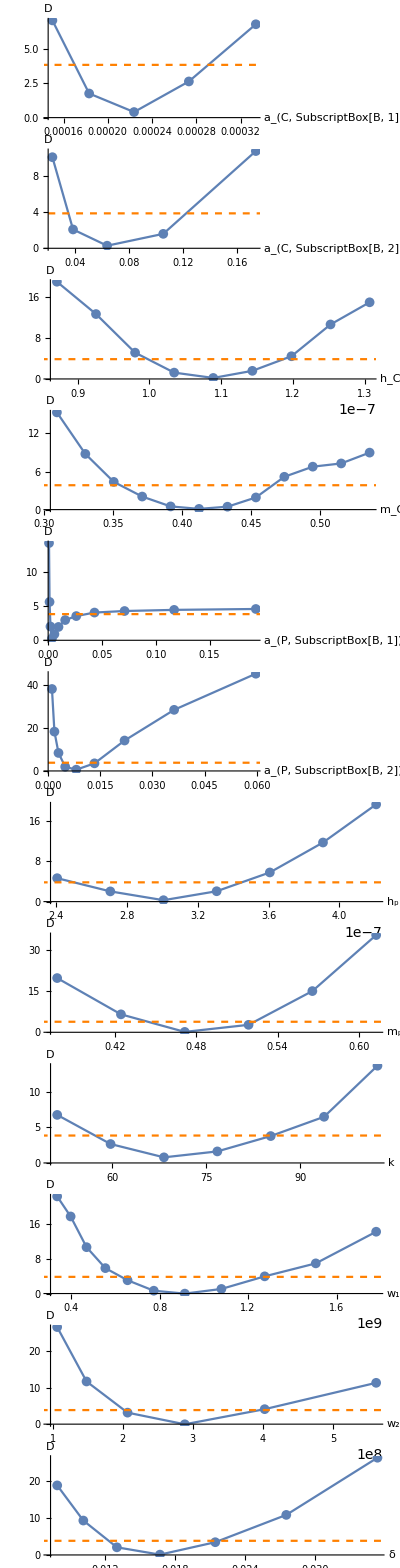

```mathematica
(*simplified mechanistic model*)
Column[{
confidenceplot["mech-simple",fitsave["mech-simple"],ac1,ⅇ^Range[-.4,.4,.2]],
confidenceplot["mech-simple",fitsave["mech-simple"],ac2,ⅇ^Range[-1,1,.5]],
confidenceplot["mech-simple",fitsave["mech-simple"],hc,Range[.8,1.2,.05]],
confidenceplot["mech-simple",fitsave["mech-simple"],mc,Range[.75,1.3,.05]],
confidenceplot["mech-simple",fitsave["mech-simple"],ap1,ⅇ^Range[-1.5,4,.5]],
confidenceplot["mech-simple",fitsave["mech-simple"],ap2,ⅇ^Range[-2,2,.5]],
confidenceplot["mech-simple",fitsave["mech-simple"],hp,Range[.8,1.4,.1]],
confidenceplot["mech-simple",fitsave["mech-simple"],mp,Range[.8,1.3,.1]],
confidenceplot["mech-simple",fitsave["mech-simple"],k,Range[.75,1.5,.125]],
confidenceplot["mech-simple",fitsave["mech-simple"],w1,ⅇ^Range[-1,2/3,1/6]],
confidenceplot["mech-simple",fitsave["mech-simple"],w2,ⅇ^Range[-1,2/3,1/3]],
confidenceplot["mech-simple",fitsave["mech-simple"],δ,ⅇ^Range[-.75,.75,.25]]
}]
```

```mathematica
(*lotka-volterra single stage fit*)
Column[{
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],r0,Range[.8,1.2,.1]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],acp,Range[.5,1.5,.25]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],apc,Range[.25,2,.25]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],lc,Range[.75,1.5,.125]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],lp,Range[.75,1.5,.125]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],k,Range[.75,1.5,.125]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],rmax,Range[.8,1.2,.1]],
confidenceplot["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],rc,Range[.75,1.5,.125]]
}];
```

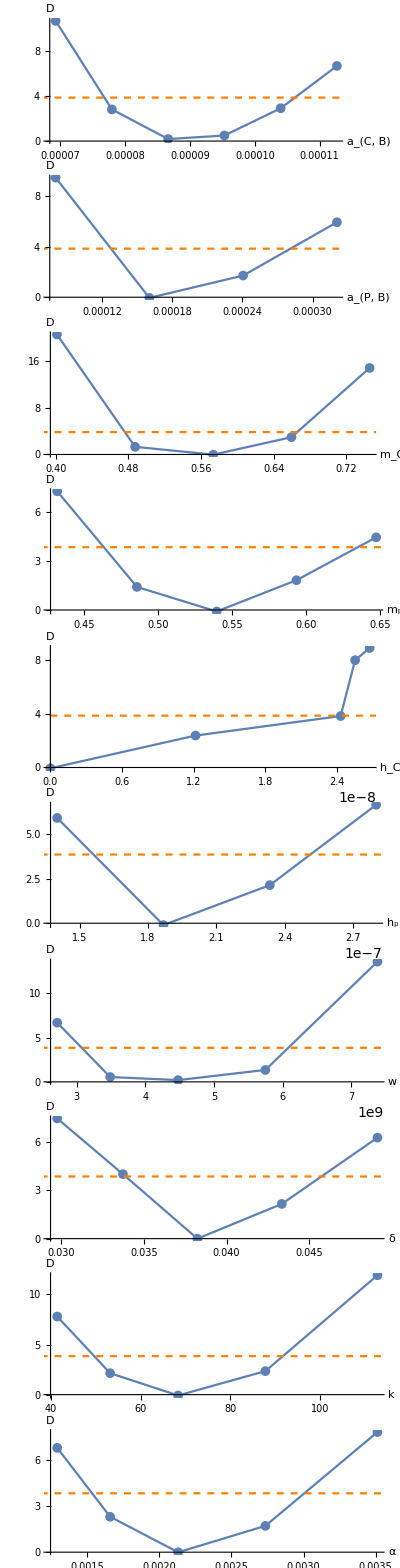

```mathematica
(*model with self-shading*)
Column[{
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],ac,Range[.8,1.3,.1]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],ap,Range[.5,2,.5]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],mc,Range[.7,1.3,.15]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],mp,Range[.8,1.2,.1]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],hc,{.001,1000,2000,2100,2200}],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],hp,Range[.75,1.5,.25]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],w,ⅇ^Range[-.5,.5,.25]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],δ,ⅇ^Range[-.25,.25,.125]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],k,ⅇ^Range[-.5,.5,.25]],
confidenceplot["huisman-weissing",fitsave["huisman-weissing"],α,ⅇ^Range[-.5,.5,.25]]
}]
```

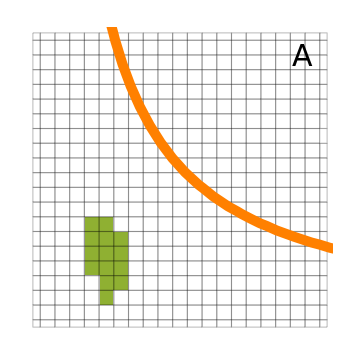

```mathematica
(*confidence region plots for lotka-volterra model with parameters acp and apc, single stage fits*)
(*create data function*)
biflist2par[model_,inifit_,par1_,par2_,range1_,range2_]:=Module[
{tofit,tokeep},
tofit=parstofit[model]/.{par1->Nothing,par2->Nothing};
tokeep=Join[parskeep[model],{par1,par2}];
Flatten[Table[Module[{par1val=i1 par1/.inifit[[2]],par2val=i2 par2/.inifit[[2]]},
{par1val,par2val,
fit2[model,(#>0&/@tofit)/.((r0>0)->(r0>-1)),tofit,tokeep,Join[inifit[[2]],testpars[model]]/.{(par1->_)->(par1->par1val),(par2->_)->(par2->par2val)},True]
}],
{i1,range1},{i2,range2}],1]
];
(*make the list*)
listLVacpapcSingleStage={#[[1]],#[[2]],-2loglh[#[[3,1]],NumberOfDataPoints]}&/@biflist2par["lotka-volterra",fitsaveONESTAGE["lotka-volterra"],acp,apc,Range[0,4,.2],Range[0,4,.2]];
(*style*)
acpapclinecol=Orange;
shadingcols={ColorData[97][3],White};
(*function to create plot*)
LVConfidenceRegionPlot[list_,bestlh_,NumberOfDataPoints_,label_]:=Show[{ListContourPlot[list,ContourShading->shadingcols,Contours->{-2loglh[bestlh,NumberOfDataPoints]+Quantile[ChiSquareDistribution[1],.95]},ImageSize->Medium,LabelStyle->16,Mesh->All,InterpolationOrder->0,MeshStyle->{{Black,Opacity[.25]}},FrameLabel->{"α_CP","α_PC"},FrameTicks->{{Automatic,None},{Automatic,None}},Frame->{{Automatic,None},{Automatic,None}},Epilog->Inset[Style[label,30],Scaled[{.9,.9}]]],
ContourPlot[acp apc==1,{acp,0,5},{apc,0,5},ContourStyle->{acpapclinecol,Thickness[.02]}]}];
(*make the plot*)(Export[outputdirectory<>"confidence-region-acp-apc-single-stage.pdf",#];#)&@LVConfidenceRegionPlot[listLVacpapcSingleStage,fitsaveONESTAGE["lotka-volterra"][[1]],NumberOfDataPoints,"A"]
```

```mathematica
(*Lotka-Volterra two stage fit*)
(*redefine function to fit model: less iterations for speed and remember previously found values*)
Clear[fitStages2];
fitStages2[model_,treatmentsANDlights_,maxday_,initialpars_,parstofit_,conditions_]:=fitStages2[model,treatmentsANDlights,maxday,initialpars,parstofit,conditions]=
Module[{nminimize,jointq},
jointq=Sum[
Module[{treatment,light},
{treatment,light}=treatlight;
q[pars[model]/.{
c0->Piecewise[{{0, treatment=="P bur"}, {c0, True}}],p0->Piecewise[{{0, treatment=="Colp"}, {p0, True}}],l->light}/.Select[initialpars,Not@MemberQ[parstofit,#[[1]]]&],
Table[{specie/.speciescodes,gettreatcroptime[{treatment,light,specie}]},{specie,species}],
sim[model][#,tcropped]&,True]],
{treatlight,treatmentsANDlights}];
Quiet@NMinimize[Flatten@{jointq,conditions},With[{val=.8#/.initialpars},{#,Min[.8val,1.5val],Max[.8val,1.5val]}]&/@Flatten@parstofit,MaxIterations->10^2,Method->{"NelderMead","PostProcess"->False}]];
(*function to create data*)
biflistStagesCombination[model_,inifit_,par_,range_,treatmentsANDlights_,tofit_,equation_]:=Table[Module[{parval=i par/. inifit,newfit},newfit=fitStages2[model,treatmentsANDlights,tcropped,Join[inifit,testpars[model]]/. {(par->_)->(par->parval)},tofit,#>0&/@(tofit/. r0->Nothing)];
{equation/. Join[{par->parval},newfit[[2]]],newfit[[1]]}],{i,range}];
(*funciton to create data, shortcut to just call L-V model*)
biflistStagesLVCombination[par_,tofit_,treatment_,range_,equation_]:=biflistStagesCombination["lotka-volterra",joinpars[joinpars[joinpars[testpars["lotka-volterra"],fitc["lotka-volterra"][[2]]],fitp["lotka-volterra"][[2]]],fitcomp["lotka-volterra"][[2]]],par,range,Table[{treatment,light},{light,lights}],tofit,equation];
(*number of datapoints in different treatments (Colp, Comp, P bur*)
NumberOfDataPointsStages[treatment_]:=Length@Flatten@Table[gettreatcroptime[{treatment,light,specie}][[All,2]],{light,lights},{specie,species}];
(*plot likelihood profile of two-stage LV fits*)
showquantsLVfromparCombination[par_,tofit_,treatment_,range_,equation_]:=
Module[{bestlh=ssqLVStages[treatment],list},
list=biflistStagesLVCombination[par,tofit,treatment,range,equation];
Show[{
ListPlot[{#[[1]],2(loglh[bestlh,NumberOfDataPointsStages[treatment]]-loglh[#[[2]],NumberOfDataPointsStages[treatment]])}&/@list,Joined->True,PlotMarkers->({Graphics`PlotMarkers[][[1,1]],10}),
AxesLabel->{equation,"D"},LabelStyle->12,
ImageSize->Medium,
ImagePadding->{{35,60},{Automatic,Automatic}},
PlotRange->Full
],
Plot[Quantile[ChiSquareDistribution[1],.95],{x,0,2Max[list[[All,1]]]},PlotStyle->{Dashed,Orange}]}
]];
(*for reference likelihood: sum of square errors for different treatments*)
ssqLVStages[treatment_]:=#["lotka-volterra"][[1]]&@Piecewise[{{fitc, treatment=="Colp"}, {fitp, treatment=="P bur"}, {fitcomp, treatment=="Comp"}}];
(*reference likelihood*)
loglhLVStages[treatment_]:=loglh[ssqLVStages[treatment],NumberOfDataPointsStages[treatment]];
(*create list of likelihoods when varying parameter par over range, given treatments and lightlevels*)
biflistStages[model_,inifit_,par_,range_,treatmentsANDlights_,tofit_]:=
Table[Module[{parval=i par/.inifit},
{parval,
fitStages2[model,treatmentsANDlights,tcropped,Join[inifit,testpars[model]]/.{(par->_)->(par->parval)},tofit,#>0&/@(tofit/.r0->Nothing)][[1]]
}],
{i,range}];
(*create this list for Lotka-Volterra two stage fits*)
biflistStagesLV[par_,tofit_,treatment_,range_]:=biflistStages["lotka-volterra",joinpars[joinpars[joinpars[testpars["lotka-volterra"],fitc["lotka-volterra"][[2]]],fitp["lotka-volterra"][[2]]],fitcomp["lotka-volterra"][[2]]],par,range,Table[{treatment,light},{light,lights}],tofit];
(*plot likelihood profile for L-V two stage fit*)
showquantsLVfrompar[par_,tofit_,treatment_,range_]:=
Module[{bestlh=ssqLVStages[treatment],list},
list=biflistStagesLV[par,tofit,treatment,range];
Show[{
ListPlot[{#[[1]],2(loglh[bestlh,NumberOfDataPointsStages[treatment]]-loglh[#[[2]],NumberOfDataPointsStages[treatment]])}&/@list,Joined->True,PlotMarkers->({Graphics`PlotMarkers[][[1,1]],10}),
AxesLabel->{par,"D"},LabelStyle->12,
ImageSize->Medium,
ImagePadding->{{35,60},{Automatic,Automatic}},
PlotRange->Full
],
Plot[Quantile[ChiSquareDistribution[1],.95],{x,0,2Max[list[[All,1]]]},PlotStyle->{Dashed,Orange}]}
]]
```

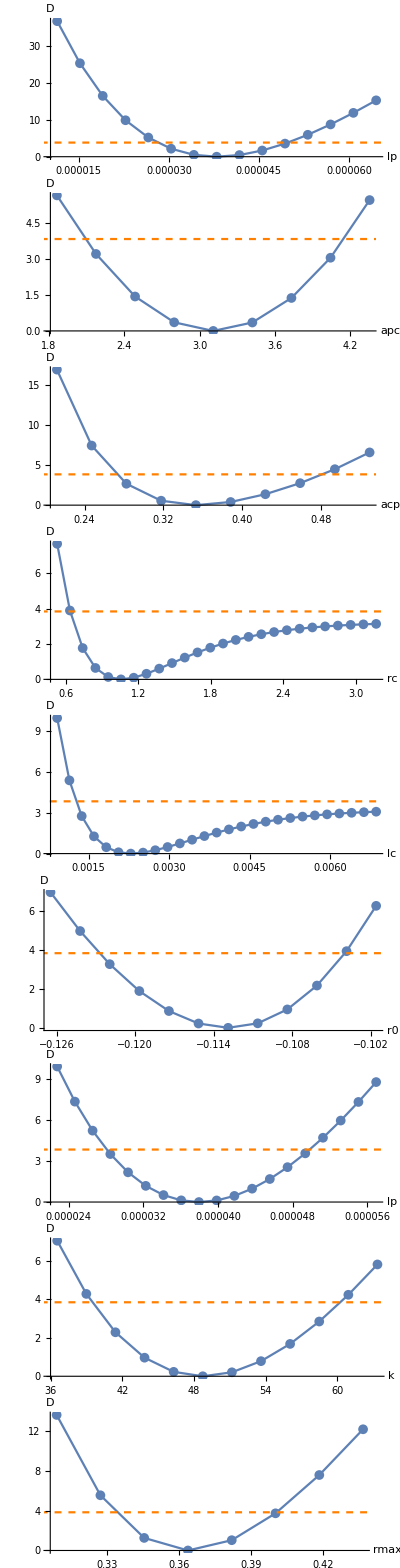

```mathematica
Column[{
showquantsLVfrompar[lp,{r0,k,rmax},"P bur",Range[.3,1.7,.1]],
showquantsLVfrompar[apc,{acp},"Comp",Range[.6,1.4,.1]],
showquantsLVfrompar[acp,{apc},"Comp",Range[.6,1.5,.1]],showquantsLVfrompar[rc,{lc},"Colp",Range[.5,3,.1]],
showquantsLVfrompar[lc,{rc},"Colp",Range[.4,3,.1]],
showquantsLVfrompar[r0,{lp,k,rmax},"P bur",Range[.9,1.12,.02]],
showquantsLVfrompar[lp,{r0,k,rmax},"P bur",Range[.6,1.5,.05]],
showquantsLVfrompar[k,{r0,lp,rmax},"P bur",Range[.75,1.3,.05]],
showquantsLVfrompar[rmax,{r0,lp,k},"P bur",Range[.85,1.2,.05]]
}]
```

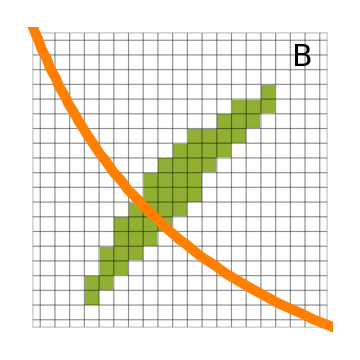

```mathematica
(*confidence region plots for lotka-volterra model with parameters acp and apc, single stage fits*)
(*function to create data list*)
biflistStages2pars[model_,inifit_,par1_,par2_,range1_,range2_,treatmentsANDlights_]:=Flatten[Table[Module[{parval1=i1 par1/. inifit,parval2=i2 par2/. inifit,likelihood},
likelihood=Sum[
Module[{treatment,light},
{treatment,light}=treatlight;
q[pars[model]/.{
c0->Piecewise[{{0, treatment=="P bur"}, {c0, True}}],p0->Piecewise[{{0, treatment=="Colp"}, {p0, True}}],l->light}/.{par1->parval1,par2->parval2}/.inifit,
Table[{specie/.speciescodes,gettreatcroptime[{treatment,light,specie}]},{specie,species}],
sim[model][#,tcropped]&,True]],
{treatlight,treatmentsANDlights}];
{parval1,parval2,likelihood}],{i1,range1},{i2,range2}],1];
(*create datalist specifically for LV model*)
biflistStagesLV2pars[par1_,par2_,treatment_,range1_,range2_]:=biflistStages2pars["lotka-volterra",joinpars[joinpars[joinpars[testpars["lotka-volterra"],fitc["lotka-volterra"][[2]]],fitp["lotka-volterra"][[2]]],fitcomp["lotka-volterra"][[2]]],par1,par2,range1,range2,Table[{treatment,light},{light,lights}]];
(*do the computation*)
listLVacpapcTwoStage={#[[1]],#[[2]],-2loglh[#[[3]],NumberOfDataPointsStages["Comp"]]}&/@biflistStagesLV2pars[acp,apc,"Comp",Range[.6,1.5,.9/20],Range[.6,1.5,.9/20]];
(*do the plot*)
(Export[outputdirectory<>"confidence-region-acp-apc-two-stage.pdf",#];#)&@LVConfidenceRegionPlot[listLVacpapcTwoStage,ssqLVStages["Comp"],NumberOfDataPointsStages["Comp"],"B"]
```

```mathematica
(*legend for acp apc plots*)
(Export[outputdirectory<>"confidence-region-acp-apc-label.pdf",#];#)&@Style[Row[{
shadingcols[[1]],"  95% confidence region                ",
Plot[.5,{x,0,1},PlotStyle->{Thickness->.3,acpapclinecol},ImageSize->20,Axes->None],"  α_CP α_PC=1"}
],FontFamily->"Arial",16]
```

RGBColor[0.560181, 0.691569, 0.194885]  95% confidence region                -Graphics-  α_CP α_PC=1